```mathematica
1+1
```

2

```mathematica
(*my constants*)
pKAH = 6.14;
dpKAH = .001 (*1/K*);
kAH = 5.6*10^6;
kAH = 15848.93192461114 (*of CO2, assuming diffusion limited, 10^(10.15-pka), valid for excess CA*);
kAH = 2.3 10^4;
(*pKCF = 6.509;*)
pKCF =6.509;
(*pKCF = 7.3;*)
(*kCF = 7.1*10^3; fluorescein, from pohl*)
kCF = 8.45*10^6; (*HPTS, from Simultaneous pH and Temperature Measurements Using Pyranine as a
Molecular Probe*)
pKM = 7.5;

kM = 2.2*10^4; (*of MEPS, from pohl*)
kM = 1584.893192461114 (*of HEPES, using 10^(10.5-pka)*);
kw = 2.5*10^-5;

pf = 16 (*μm/s*);
pf = 1.3 10^-4 (*m/s*)
c = 1 (*μF/cm^2*);
c = 10^-2 (*F/m^2*)
Pprot = 3.5*10^-5 (*cm/s*);
Pprot = 3.5*10^-7 (*m/s*);
F = 96485.33212 (*C/mol, faraday's constant*);
RR = 8.314 (*J/K mol, gas constant*)
H20 = 55.5 (*mol/L*);
R = 10.*10^-6 (*m*);
V = 4/3 π R^3;
S = 4 π R^2;
AHout = .034/2(*M, solubility of Subscript[CO, 2]*);
AHout = (.033)/(1+10^(pH-pKAH))/2;
CFtot = 0.187 10^-3 (*M, concentration of fluorophore*);
Mtot = 2 10^-3 (*M, concentration of buffering molecule*);
pH = 7.5 (*initial only*);
T = 300 (*K*);
Hout = 10^-pH;
(*initial conditions*)
H0 = 10^-7.5;
(*cc[0] == 10^-7.5,*)
OH0 = 10^-6.5;
A0 = 0.0;
AH0 = 0.0;
CF0 = CFtot/(1+10^(pKCF-pH));
CFH0=CFtot/(1+10^(pH-pKCF));
MH0 = Mtot/(1+10^(pH-pKM));
M0 = Mtot/(1+10^(pKM-pH));
initCond = {AH[t]-> AH0, A[t] ->A0, H[t]->H0, OH[t] -> OH0, MH[t] -> MH0, M[t]->M0, CF[t]->CF0, CFH[t]->CFH0};
```

0.00013

1/100

8.314

```mathematica
(*pohl's constants*)
pKAH = 3.75;
dpKAH = .001 (*1/K*);
kAH = 5.6*10^6;
kAH = 15848.93192461114 (*of CO2, assuming diffusion limited, 10^(10.15-pka), valid for excess CA*);
pKCF = 6.509;
dpKCF = -.005;
kCF = 7.1*10^3; (*fluorescein, from pohl*)
(*kCF = 8.45*10^6;*) (*HPTS, from Simultaneous pH and Temperature Measurements Using Pyranine as a
Molecular Probe*)
pKM = 6.15;
dpKM = -.011;
kM = 2.2*10^4; (*of MEPS, from pohl*)
(*kM = 1584.893192461114*) (*of HEPES, using 10^(10.5-pka);*)
kw = 2.5*10^-5;
dpKw = -.033;
pf = 16 (*μm/s*);
pf = 10. 10^-6 (*m/s*)
c = 1. (*μF/cm^2*);
c = 1.*10^-2 (*F/m^2*)
Pprot = 3.5*10^-5 (*cm/s*);
Pprot = 3.5*10^-7 (*m/s*);
F = 96485.33212 (*C/mol, faraday's constant*);
RR = 8.314 (*J/K mol, gas constant*)
H20 = 55.5 (*mol/L*);
R = 10.*10^-6 (*m*);
R = 55.0 10^-9(*m*);
V = 4/3 π R^3;
S = 4 π R^2;
AHoutTot = .01(*M, solubility of Subscript[CO, 2]*);
AHout = AHoutTot/(1+10^(pH-pKAH))
CFtot = 0.5 10^-3 (*M, concentration of fluorophore*);
Mtot = 10. 10^-3 (*M, concentration of buffering molecule*);
pH = 7.0 (*initial only*);
T = 300 (*K*);
Hout = 10^-pH;
(*initial conditions*)
H0 = 10^-pH;
(*cc[0] == 10^-7.5,*)
OH0 = 10^(-(14-pH));
A0 = 0.0;
AH0 = 0.0;
CF0 = CFtot/(1+10^(pKCF-pH));
CFH0=CFtot/(1+10^(pH-pKCF));
MH0 = Mtot/(1+10^(pH-pKM));
M0 = Mtot/(1+10^(pKM-pH));
initCond = {AH[t]-> AH0, A[t] ->A0, H[t]->H0, OH[t] -> OH0, MH[t] -> MH0, M[t]->M0, CF[t]->CF0, CFH[t]->CFH0};
```

0.00001

0.01

8.314

5.62025×10^-6

```mathematica
fred = ParametricNDSolveValue[{
AH'[t] == -kAH*AH  [t] + kAH*10^pKAH*A[t]*H[t]- S/V*Pm*(AH[t] - AHout),
A'[t] == kAH*AH[t]-kAH*10^pKAH*A[t]*H[t],
OH'[t] == kw*H20- H20*kw*10^14*OH[t]*H[t],
(*cc'[t] == -((- cc[t]*F)/(S*c)*S*Pprot*F)/(R*T*V)(H[t]-Hout*Exp[(-(- cc[t]*F)/(S*c)*F)/(R*T)])/(1-Exp[(-(- cc[t]*F)/(S*c)*F)/(R*T)]),*)

H'[t] == kw*H20- H20*kw*10^14*OH[t]*H[t]+ kAH*AH[t]- kAH*10^pKAH*A[t]*H[t]+kCF*CFH[t]- kCF*10^pKCF*CF[t]*H[t]+kM*MH[t] - kM*10^pKM*M[t]*H[t]+-((- H[t]*F)/(S*c)*S*Pprot*F)/(RR*T)((H[t]-Hout)*Exp[(-(- H[t]*F)/(S*c)*F)/(RR*T)*V])/(1-Exp[(-(- H[t]*F)/(S*c)*F)/(RR*T)*V]),
CFH'[t] == -kCF*CFH[t]+ kCF*10^pKCF*CF[t]*H[t],
CF'[t] == -(-kCF*CFH[t]+ kCF*10^pKCF*CF[t]*H[t]),
MH'[t] == -kM*MH[t]+ kM*10^pKM*M[t]*H[t],
M'[t] == -(-kM*MH[t]+ kM*10^pKM*M[t]*H[t]),
(*initial conditions*)
H[0] == H0,
(*cc[0] == 10^-7.5,*)
OH[0] == OH0,
A[0] == A0,
AH[0] == AH0,
CF[0] ==CF0,
CFH[0]==CFH0,
MH[0] ==MH0,
M[0] == M0},
{A, AH, M, MH, CF, CFH, H, OH},
{t, 0, 2},
{Pm}, WorkingPrecision->30]
```

ParametricFunction[<>]

```mathematica
george = ParametricNDSolveValue[{
AH'[t] == -kAH*AH  [t] + kAH*10^pKAH*A[t]*H[t]- S/V*Pm*(AH[t] - AHout),
A'[t] == kAH*AH[t]-kAH*10^pKAH*A[t]*H[t],
OH'[t] == kw*H20- H20*kw*10^14*OH[t]*H[t],
(*cc'[t] == -((- cc[t]*F)/(S*c)*S*Pprot*F)/(R*T*V)(H[t]-Hout*Exp[(-(- cc[t]*F)/(S*c)*F)/(R*T)])/(1-Exp[(-(- cc[t]*F)/(S*c)*F)/(R*T)]),*)

H'[t] == kw*H20- H20*kw*10^14*OH[t]*H[t]+ kAH*AH[t]- kAH*10^pKAH*A[t]*H[t]+kCF*CFH[t]- kCF*10^pKCF*CF[t]*H[t]+kM*MH[t] - kM*10^pKM*M[t]*H[t]+-((- H[t]*F)/(S*c)*S*Pprot*F)/(RR*T)((H[t]-Hout)*Exp[(-(- H[t]*F)/(S*c)*F)/(RR*T)*V])/(1-Exp[(-(- H[t]*F)/(S*c)*F)/(RR*T)*V]),
CFH'[t] == -kCF*CFH[t]+ kCF*10^pKCF*CF[t]*H[t],
CF'[t] == -(-kCF*CFH[t]+ kCF*10^pKCF*CF[t]*H[t]),
MH'[t] == -kM*MH[t]+ kM*10^pKM*M[t]*H[t],
M'[t] == -(-kM*MH[t]+ kM*10^pKM*M[t]*H[t]),
(*initial conditions*)
H[0] == H0,
(*cc[0] == 10^-7.5,*)
OH[0] == OH0,
A[0] == A0,
AH[0] == AH0,
CF[0] ==CF0,
CFH[0]==CFH0,
MH[0] ==MH0,
M[0] == M0,
VV[0] ==V},
{A, AH, M, MH, CF, CFH, H, OH, VV},
{t, 0, 2},
{Pm}, WorkingPrecision->30]
```

```mathematica
{AH'[t] == -kAH*AH  [t] + kAH*10^pKAH*A[t]*H[t]- S/V*Pm*(AH[t] - AHout),
A'[t] == kAH*AH[t]-kAH*10^pKAH*A[t]*H[t],
OH'[t] == kw*H20- H20*kw*10^14*OH[t]*H[t],
(*cc'[t] == -((- cc[t]*F)/(S*c)*S*Pprot*F)/(R*T*V)(H[t]-Hout*Exp[(-(- cc[t]*F)/(S*c)*F)/(R*T)])/(1-Exp[(-(- cc[t]*F)/(S*c)*F)/(R*T)]),*)

H'[t] == kw*H20- H20*kw*10^14*OH[t]*H[t]+ kAH*AH[t]- kAH*10^pKAH*A[t]*H[t]+kCF*CFH[t]- kCF*10^pKCF*CF[t]*H[t]+kM*MH[t] - kM*10^pKM*M[t]*H[t](*+-((- H[t]*F)/(S*c)*S*Pprot*F)/(R*T*V)((H[t]-Hout)*Exp[(-(- H[t]*F)/(S*c)*F)/(R*T)])/(1-Exp[(-(- H[t]*F)/(S*c)*F)/(R*T)])*),
CFH'[t] == -kCF*CFH[t]+ kCF*10^pKCF*CF[t]*H[t],
CF'[t] == -(-kCF*CFH[t]+ kCF*10^pKCF*CF[t]*H[t]),
MH'[t] == -kM*MH[t]+ kM*10^pKM*M[t]*H[t],
M'[t] == -(-kM*MH[t]+ kM*10^pKM*M[t]*H[t])}/.initCond
```

{AH'[t]==0.+545455. Pm,A'[t]==0.,OH'[t]==0.,H'[t]==-1.38778×10^-15,CFH'[t]==-5.55112×10^-17,CF'[t]==5.55112×10^-17,MH'[t]==1.77636×10^-15,M'[t]==-1.77636×10^-15}

```mathematica
Table[fred[1.80*10^-5][[5]][t+.06]/fred[1.80*10^-5][[5]][.06], {t, 0, 2, .05}]
```

ParametricNDSolveValue::precw: The precision of the differential equation ({{AH'[t$28537]==-300000. Pm$28536 (-0.000690126+AH[t$28537])-2300. AH[t$28537]+3.17488×10^9 A[t$28537] H[t$28537],A'[t$28537]==2300. AH[t$28537]-3.17488×10^9 A[t$28537] H[t$28537],OH'[t$28537]==0.0013875-1.3875×10^11 H[t$28537] OH[t$28537],«10»,CFH[0]==0.000017323,MH[0]==0.0005,M[0]==0.0005},{},{},{},{}}) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {2.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

{1.,0.867096,0.72235,0.604757,0.522605,0.467012,0.42889,0.402138,0.382946,0.368921,0.35852,0.350718,0.344813,0.340312,0.336863,0.33421,0.332161,0.330575,0.329346,0.328391,0.327649,0.327072,0.326622,0.326272,0.326,0.325787,0.325622,0.325493,0.325393,0.325315,0.325255,0.325208,0.325172,0.325144,0.325122,0.325106,0.325094,0.325084,0.325077,0.325072,0.325068}

```mathematica
Table[t, {t, 0, 2, .05}]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.}

```mathematica
plotData = Table[{t,-Log[10,fred[1.80*10^-5][[7]][t]]}, {t, 0, 1, .05}];
```

ParametricNDSolveValue::precw: The precision of the differential equation ({{AH'[t$5843]==-300000. Pm$5842 (-0.000690126+AH[t$5843])-15848.9 AH[t$5843]+2.18776×10^10 A[t$5843] H[t$5843],A'[t$5843]==15848.9 AH[t$5843]-2.18776×10^10 A[t$5843] H[t$5843],OH'[t$5843]==0.0013875-1.3875×10^11 H[t$5843] OH[t$5843],«10»,CFH[0]==0.000017323,MH[0]==0.0005,M[0]==0.0005},{},{},{},{}}) is less than WorkingPrecision (30.).

```mathematica
plotData
```

{{0.,7.5},{0.05,7.21704},{0.1,6.94714},{0.15,6.70929},{0.2,6.52889},{0.25,6.40255},{0.3,6.31465},{0.35,6.25237},{0.4,6.20733},{0.45,6.17417},{0.5,6.14942},{0.55,6.13075},{0.6,6.11656},{0.65,6.1057},{0.7,6.09736},{0.75,6.09092},{0.8,6.08594},{0.85,6.08209},{0.9,6.07909},{0.95,6.07676},{1.,6.07495}}

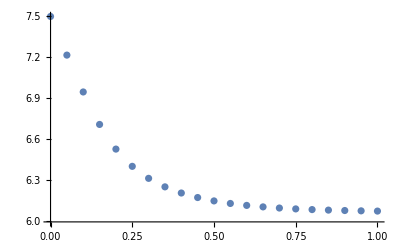

```mathematica
ListPlot[plotData]
```

```mathematica
ListPlot
```

```mathematica
S/V
```

5.45455×10^7

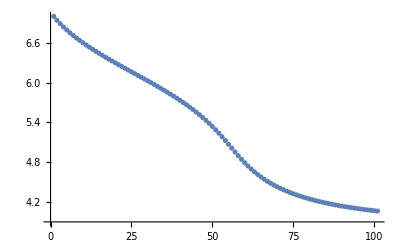

```mathematica
ListPlot[{7.,6.94261145956224,6.890021923789262,6.841400294612775,6.79604450002847,6.753415595863337,6.71309030216637,6.674729593302964,6.638057232621401,6.602844693040797,6.56890030665904,6.5360612908120395,6.504187776770838,6.4731582610457,6.442866086687075,6.413216679366165,6.384125350128479,6.355515519664552,6.327317269204268,6.299466138606602,6.271902116899896,6.244568781382938,6.2174125516759915,6.1903820328762675,6.163427424579578,6.13649998043393,6.109551502030068,6.08253385482128,6.0553984946002855,6.028095994306733,6.0005755617791365,5.972784537728671,5.9446678663319945,5.916167528851185,5.887221930633848,5.857765234770995,5.827726634720627,5.797029562435172,5.765590833140353,5.733319737285868,5.700117105678794,5.665874400550541,5.630472927154798,5.59378333072938,5.555665652423585,5.515970384125996,5.474541214122307,5.431220502698931,5.3858589701920705,5.338331527426251,5.288561359944372,5.236553691345177,5.18243808479687,5.126512659096699,5.06927557173832,5.0114227591147325,4.953794637957198,4.897274099349558,4.842665319279166,4.790596062579656,4.741472487898285,4.69548719455982,4.652660846268701,4.612894388417514,4.576016415105973,4.541819316911696,4.510083818519856,4.480594112041186,4.4531462963133635,4.4275524362086385,4.403641937326113,4.381261376317208,4.360273511366413,4.340555913401705,4.321999474862385,4.3045069385462105,4.287991519790771,4.27237565451461,4.2575898825661005,4.243571863242639,4.230265513531761,4.217620257024144,4.205590370755041,4.194134417722055,4.183214753817134,4.172797099062624,4.162850164315036,4.153345325707479,4.144256340213825,4.135559096623514,4.127231397047587,4.119252764788001,4.111604275004554,4.104268405134264,4.0972289024594275,4.090470666589388,4.083979644949602,4.077742739629873,4.0717477241817095,4.065983169142015,4.060438375233468}]
```

```mathematica
-Log[
```

Values at t -> ∞

```mathematica
AHinf = fred[.001][[2]][1];
Ainf = fred[.001][[1]][1];
Minf = fred[.001][[3]][1];
MHinf = fred[.001][[4]][1];
CFinf = fred[.001][[5]][1];
CFHinf = fred[.001][[6]][1];
Hinf = fred[.001][[7]][1];
OHinf = fred[.001][[8]][1];
```

ParametricNDSolveValue::precw: The precision of the differential equation ({{AH'[t$72790]==-300000. Pm$72789 (-0.017+AH[t$72790])-5.6×10^6 AH[t$72790]+1.11735×10^13 A[t$72790] H[t$72790],A'[t$72790]==5.6×10^6 AH[t$72790]-1.11735×10^13 A[t$72790] H[t$72790],OH'[t$72790]==0.0013875-1.3875×10^11 H[t$72790] OH[t$72790],«10»,CFH[0]==0.0000409159,MH[0]==0.005,M[0]==0.005},{},{},{},{}}) is less than WorkingPrecision (20.).

```mathematica
-Log[10,(Hinf Ainf)/AHinf]
```

3.7500000000000000168

```mathematica
-Log[10, (Hinf Minf)/MHinf]
```

6.1500000000000003366

```mathematica
-Log[10, (CFinf Hinf)/CFHinf]
```

6.4500000000000001843

```mathematica
-Log[10, Hinf OHinf]
```

13.9999999999999999807

```mathematica
AHinf
```

0.016999999999999608976

```mathematica
AHout
```

0.017

```mathematica
-Log[10, Hinf]
```

5.78417279395953019717

```mathematica
CFinf/CFHinf
```

0.2158603087763538948

```mathematica
H0
```

3.16228×10^-8

```mathematica
kAH*AH[t]-kAH*10^pKAH*A[t]/.{AH[t]->fred[.001][[2]][.01], A[t]->fred[.001][[1]][.01], H[t]->fred[.001][[7]][.01], Pm -> .001}
```

-1.77636×10^-15

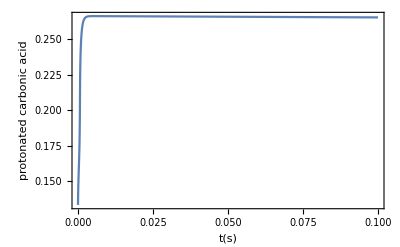

```mathematica
Plot[-Log[fred[.000034][[7]][t],10], {t, 0, .1},  PlotRange->All, Frame->True, FrameLabel->{"t(s)", "protonated  carbonic acid", "[H_2CO_3]"}]
```

InterpolatingFunction::dmval: Input value {2.04286×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

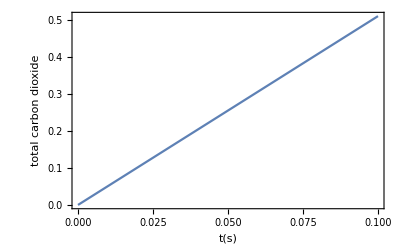

```mathematica
Plot[fred[.000034][[1]][t]+fred[.001][[2]][t], {t, 0, .1},  PlotRange->All, Frame->True, FrameLabel->{"t(s)", "total carbon dioxide", "[H_2CO_3]"}]
```

InterpolatingFunction::dmval: Input value {2.04286×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

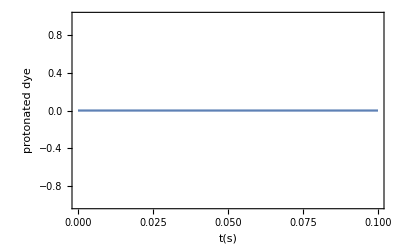

```mathematica
Plot[fred[.001][[6]][t],  {t, 0, 0.1},PlotRange->All, Frame->True, FrameLabel->{"t(s)", "protonated dye", "[H_2CO_3]"}]
```

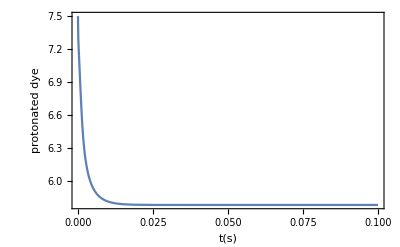

```mathematica
Plot[-Log[10,fred[.001][[7]][t]],  {t, 0, 0.1},PlotRange->All, Frame->True, FrameLabel->{"t(s)", "protonated dye", "[H_2CO_3]"}]
```

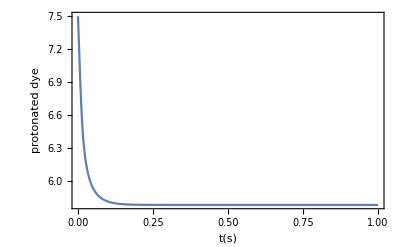

```mathematica
Plot[-Log[10,fred[.0001][[7]][t]],  {t, 0, 1},PlotRange->All, Frame->True, FrameLabel->{"t(s)", "protonated dye", "[H_2CO_3]"}]
```

```mathematica
Table[-Log[10,fred[.00001][[7]][t]], {t, 0, 1, .01}]
```

{7.5,7.41867,7.33888,7.25988,7.18138,7.10341,7.02629,6.95066,6.87736,6.80726,6.74113,6.67947,6.6225,6.57019,6.5223,6.47854,6.43851,6.40187,6.36824,6.33732,6.3088,6.28244,6.25801,6.2353,6.21416,6.19442,6.17595,6.15864,6.14238,6.12709,6.11268,6.09908,6.08623,6.07406,6.06254,6.05161,6.04123,6.03136,6.02197,6.01302,6.0045,5.99637,5.9886,5.98118,5.97409,5.9673,5.96081,5.95459,5.94862,5.94291,5.93742,5.93216,5.92711,5.92225,5.91759,5.9131,5.90879,5.90464,5.90064,5.8968,5.89309,5.88953,5.88609,5.88278,5.87959,5.87651,5.87354,5.87067,5.86791,5.86524,5.86266,5.86017,5.85777,5.85545,5.85321,5.85104,5.84895,5.84693,5.84497,5.84308,5.84125,5.83949,5.83778,5.83612,5.83452,5.83297,5.83148,5.83003,5.82862,5.82727,5.82595,5.82468,5.82345,5.82225,5.8211,5.81998,5.81889,5.81784,5.81683,5.81584,5.81489}

```mathematica
Table[fred[.00001][[5]][t]/CFtot, {t, 0, 1, .01}]
```

{0.918168,0.903155,0.885847,0.866114,0.843726,0.818556,0.790663,0.760361,0.728243,0.695119,0.661889,0.629387,0.59827,0.568973,0.541726,0.516596,0.493541,0.472454,0.453193,0.4356,0.41952,0.404805,0.391317,0.378931,0.367535,0.357029,0.347323,0.33834,0.330008,0.322266,0.31506,0.308339,0.302062,0.296189,0.290686,0.285522,0.28067,0.276104,0.271802,0.267744,0.263912,0.26029,0.256861,0.253613,0.250534,0.247611,0.244835,0.242195,0.239684,0.237293,0.235014,0.232842,0.230769,0.228791,0.2269,0.225093,0.223365,0.221712,0.220129,0.218613,0.217159,0.215766,0.21443,0.213148,0.211917,0.210736,0.2096,0.208509,0.20746,0.206452,0.205481,0.204548,0.203649,0.202784,0.201951,0.201148,0.200375,0.19963,0.198911,0.198218,0.19755,0.196906,0.196284,0.195684,0.195104,0.194545,0.194005,0.193483,0.19298,0.192493,0.192023,0.191569,0.19113,0.190705,0.190295,0.189898,0.189514,0.189143,0.188784,0.188437,0.188101}

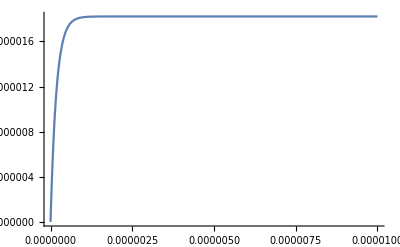

```mathematica
Plot[fred[.001][[2]][t], {t, 0, .001}, PlotRange->All]
```

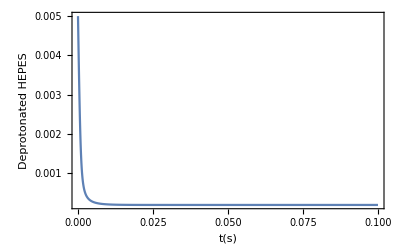

```mathematica
Plot[fred[.001][[3]][t], {t, 0, .1}, PlotRange->All, Frame->True, FrameLabel->{"t(s)", "Deprotonated HEPES", "[HEPES^-]"}]
```

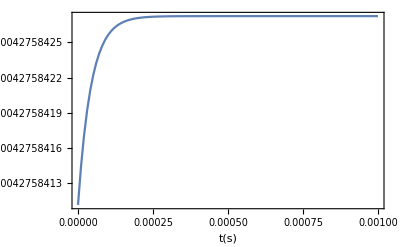

```mathematica
Plot[fred[.001][[4]][t], {t, 0, .001}, PlotRange->All, Frame->True, FrameLabel->{"t(s)", "Protonated HEPES", "[HEPES]"}]
```

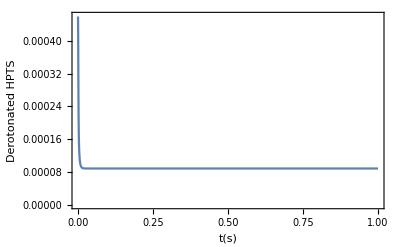

```mathematica
Plot[fred[.001][[5]][t], {t, 0, 1}, Frame->True, FrameLabel->{"t(s)", "Derotonated HPTS", "[HPTS]"}, PlotRange->{0, .00046}]
```

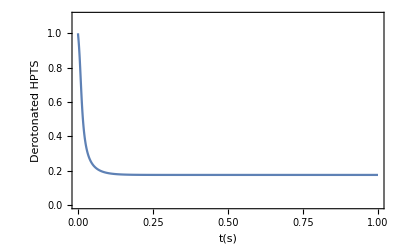

```mathematica
Plot[fred[.0001][[5]][t]/fred[.00001][[5]][0], {t, 0, 1}, Frame->True, FrameLabel->{"t(s)", "Derotonated HPTS", "[HPTS]"}, PlotRange->{0, 1.1}]
```

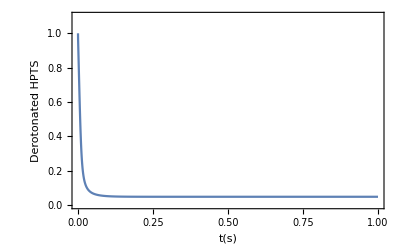

```mathematica
Plot[fred[.0001][[5]][t]/fred[.00001][[5]][0], {t, 0, 1}, Frame->True, FrameLabel->{"t(s)", "Derotonated HPTS", "[HPTS]"}, PlotRange->{0, 1.1}]
```

```mathematica
2^15
```

32768

```mathematica
2^20*.0000001
```

0.104858

```mathematica
Table [5*j*10.^-6,{j, 1, 50}]
```

{5.×10^-6,0.00001,0.000015,0.00002,0.000025,0.00003,0.000035,0.00004,0.000045,0.00005,0.000055,0.00006,0.000065,0.00007,0.000075,0.00008,0.000085,0.00009,0.000095,0.0001,0.000105,0.00011,0.000115,0.00012,0.000125,0.00013,0.000135,0.00014,0.000145,0.00015,0.000155,0.00016,0.000165,0.00017,0.000175,0.00018,0.000185,0.00019,0.000195,0.0002,0.000205,0.00021,0.000215,0.00022,0.000225,0.00023,0.000235,0.00024,0.000245,0.00025}

```mathematica
Table [5.*j*10^-6, {j, 0, 51}]
```

{0.,5.×10^-6,0.00001,0.000015,0.00002,0.000025,0.00003,0.000035,0.00004,0.000045,0.00005,0.000055,0.00006,0.000065,0.00007,0.000075,0.00008,0.000085,0.00009,0.000095,0.0001,0.000105,0.00011,0.000115,0.00012,0.000125,0.00013,0.000135,0.00014,0.000145,0.00015,0.000155,0.00016,0.000165,0.00017,0.000175,0.00018,0.000185,0.00019,0.000195,0.0002,0.000205,0.00021,0.000215,0.00022,0.000225,0.00023,0.000235,0.00024,0.000245,0.00025,0.000255}

```mathematica
Table [fred[5.*j*10^-6][[5]][t]/fred[.00001][[5]][0], {j, 1, 50},{t, 0, 1.5, 0.01}]
```

ParametricNDSolveValue::precw: The precision of the differential equation ({{AH'[t$37084]==-300000. Pm$37083 (-0.017+AH[t$37084])-15848.9 AH[t$37084]+3.16228×10^10 A[t$37084] H[t$37084],A'[t$37084]==15848.9 AH[t$37084]-3.16228×10^10 A[t$37084] H[t$37084],OH'[t$37084]==0.0013875-1.3875×10^11 H[t$37084] OH[t$37084],«10»,CFH[0]==0.0000463182,MH[0]==0.005,M[0]==0.005},{},{},{},{}}) is less than WorkingPrecision (30.).

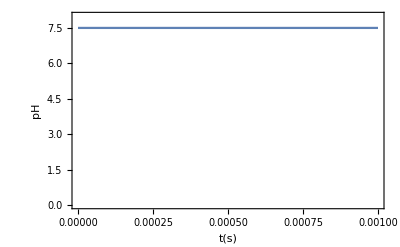

```mathematica
Plot[-Log[10,fred[.001][[7]][t]], {t, 0, .001}, Frame->True, FrameLabel->{"t(s)", "pH", "pH"}, PlotRange->{0,8}]
```

```mathematica
Log[10,fred[.001][[7]][0]]
```

-7.500000000000000019346419041672898363365

```mathematica
Log[10^-7.5]
```

-0.133333

```mathematica
Log
```

```mathematica
CFtot/(1+10^(pH-pKCF))
```

0.0000409159

```mathematica
CFtot/(1+10^(pKCF-pH))
```

0.000459084

```mathematica
Mtot/(1+10^(pKM-pH))
```

0.000957242

```mathematica
Mtot/(1+10^(pH-pKM))
```

0.0000427584

InterpolatingFunction::dmval: Input value {0.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.

```mathematica
Clear[fred]
```

```mathematica
pfun=ParametricNDSolveValue[{y'[t]==a x[t],x'[t]==-y[t],x[0]==0,y[0]==1},{y,x},{t,0,10},{a}]
```

ParametricFunction[<>]

```mathematica
pfun[5][[1]][1]
```

4.73167

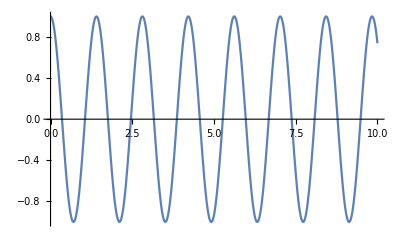

```mathematica
Plot[pfun[20][[1]][t], {t, 0, 10}]
```

```mathematica
Log[2.,10]
```

3.32193

```mathematica
Simplify[-Log[10^(10.5-pK)/(2. 10^10), 10.], pK>0]
```

-1./(0.19897-1. pK)

```mathematica
ParametricNDSolveValue
```

```mathematica
Solve[MH/(Mtot - MH)==10^(pkm-pH), MH]
```

```mathematica
{{MH->(10^pkm Mtot)/(10^pH+10^pkm)}}
```

```mathematica
Simplify[Mtot - (10^pkm Mtot)/(10^pH+10^pkm)]
```

(10^pH Mtot)/(10^pH+10^pkm)

```mathematica
R/3 (1+10^(pH-pKAH-1))
```

8.61631×10^-6

```mathematica
pkAH
```

pkAH

```mathematica
pH
```

7.5